```mathematica
fftw=Import[FileNameJoin[{NotebookDirectory[],"FFTW.csv"}]]//Transpose;
fftwFit=NonlinearModelFit[{#[[1]],Log[#[[2]]]}&/@fftw,Log[a*x^b*Log[x]+c],{{a,5.618*10^-10},{b,1.17},{c,0}},x];
naive=Import[FileNameJoin[{NotebookDirectory[],"naiveDFT.csv"}]]//Transpose;
naiveFit=NonlinearModelFit[naive,a*x^b,{{a,6.6*10^-8},{b,2}},x];
naiveIter=Import[FileNameJoin[{NotebookDirectory[],"naiveDFTIter.csv"}]]//Transpose;
naiveIterFit=NonlinearModelFit[naiveIter,a*x^b,{{a,6.6*10^-8},{b,2}},x];
simple=Import[FileNameJoin[{NotebookDirectory[],"simpleDFT.csv"}]]//Transpose;
simpleFit=NonlinearModelFit[{#[[1]],Log[#[[2]]]}&/@simple,Log[Abs[a*x^b]],{{a,5.7*10^-7},{b,1.1}},x];
matlab=Import[FileNameJoin[{NotebookDirectory[],"matlab.csv"}]];
matlabFit=NonlinearModelFit[{#[[1]],Log[#[[2]]]}&/@matlab,Log[a*x^b*Log[x]+c],{{a,5.618*10^-10},{b,1.17},{c,0}},x];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

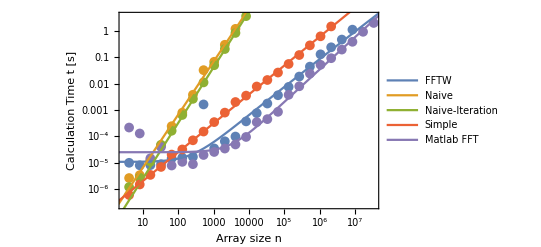

```mathematica
g=Legended[
Show[{
ListLogLogPlot[{fftw,naive,naiveIter,simple,matlab},PlotStyle->(Directive[{ColorData[97]@#,PointSize[0.0175]}]&/@Range[5]),PlotRange->All],
LogLogPlot[Evaluate[{Exp[fftwFit["BestFit"]],naiveFit["BestFit"],naiveIterFit["BestFit"],Exp[simpleFit["BestFit"]],Exp[matlabFit["BestFit"]]}],{x,2,5*10^7},PlotStyle->(ColorData[97]/@Range[5])]
},FrameLabel->Thread[Style[{"Array size n","Calculation Time t [s]"},FontSize->16]]]
,LineLegend[(ColorData[97]/@Range[5]),Thread[Style[{"FFTW","Naive","Naive-Iteration","Simple","Matlab FFT"},FontSize->14]]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Comparison.pdf"}],g]
```

C:\Users\Jelle\Desktop\coding\ComputationalPhotonics\Excercise_01\A2\data\Comparison.pdf

```mathematica
#["ParameterTable"]&/@{fftwFit,naiveFit,naiveIterFit,simpleFit,matlabFit}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 8.97788×10^-9 | 9.3775×10^-9 | 0.957385 | 0.350398
b | 0.97267 | 0.0888784 | 10.9438 | 1.20789×10^-9
c | 0.000010993 | 4.80735×10^-6 | 2.2867 | 0.0338621, | Estimate | Standard Error | t-Statistic | P-Value
a | 6.89673×10^-8 | 1.30597×10^-8 | 5.28092 | 0.000506486
b | 2.0017 | 0.022887 | 87.4601 | 1.69235×10^-14, | Estimate | Standard Error | t-Statistic | P-Value
a | 2.11774×10^-8 | 1.15152×10^-9 | 18.3908 | 4.865×10^-9
b | 2.10164 | 0.00606001 | 346.805 | 9.7743×10^-22, | Estimate | Standard Error | t-Statistic | P-Value
a | -1.72151×10^-7 | 1.16583×10^-8 | -14.7665 | 1.67555×10^-11
b | 1.09016 | 0.00794346 | 137.24 | 1.22328×10^-28, | Estimate | Standard Error | t-Statistic | P-Value
a | 3.02732×10^-10 | 3.29946×10^-10 | 0.91752 | 0.369288
b | 1.15298 | 0.0808318 | 14.2639 | 2.82771×10^-12
c | 0.0000254717 | 6.61777×10^-6 | 3.84899 | 0.000931651}